```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian System eta Data\\beta_0.06_NM_eta_vary"];
LNDataeta001=ReadList["LNData_NM_eta_0.01.txt"];
LNDataeta002=ReadList["LNData_NM_eta_0.02.txt"];
LNDataeta003=ReadList["LNData_NM_eta_0.03.txt"];
LNDataeta004=ReadList["LNData_NM_eta_0.04.txt"];
LNDataeta005=ReadList["LNData_NM_eta_0.05.txt"];
LNDataeta006=ReadList["LNData_NM_eta_0.06.txt"];
LNDataeta007=ReadList["LNData_NM_eta_0.07.txt"];
```

```mathematica
eta001=Table[Table[{LNDataeta001[[pair]][[pt]][[1]], 0.01, LNDataeta001[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
eta002=Table[Table[{LNDataeta002[[pair]][[pt]][[1]], 0.02, LNDataeta002[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
eta003=Table[Table[{LNDataeta003[[pair]][[pt]][[1]], 0.03, LNDataeta003[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
eta004=Table[Table[{LNDataeta004[[pair]][[pt]][[1]], 0.04, LNDataeta004[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
eta005=Table[Table[{LNDataeta005[[pair]][[pt]][[1]], 0.05, LNDataeta005[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
eta006=Table[Table[{LNDataeta006[[pair]][[pt]][[1]], 0.06, LNDataeta006[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
eta007=Table[Table[{LNDataeta007[[pair]][[pt]][[1]], 0.07, LNDataeta007[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
```

```mathematica
(* LN12, LN13=LN24, LN14=LN23, LN34 *)
etaData={
{eta001[[1]], eta001[[2]], eta001[[3]], eta001[[6]]},
{eta002[[1]], eta002[[2]], eta002[[3]], eta002[[6]]},
{eta003[[1]], eta003[[2]], eta003[[3]], eta003[[6]]},
{eta004[[1]], eta004[[2]], eta004[[3]], eta004[[6]]},
{eta005[[1]], eta005[[2]], eta005[[3]], eta005[[6]]},
{eta006[[1]], eta006[[2]], eta006[[3]], eta006[[6]]},
{eta007[[1]], eta007[[2]], eta007[[3]], eta007[[6]]}};
(* Modified Data Order: LN34, LN12, LN14=LN23, LN13=LN24*)
etaData={
{eta001[[6]], eta001[[1]], eta001[[3]],eta001[[2]]},
{eta002[[6]], eta002[[1]], eta002[[3]], eta002[[2]]},
{eta003[[6]], eta003[[1]], eta003[[3]],eta003[[2]]},
{eta004[[6]], eta004[[1]], eta004[[3]],eta004[[2]]},
{eta005[[6]], eta005[[1]], eta005[[3]],eta005[[2]]},
{eta006[[6]], eta006[[1]], eta006[[3]],eta006[[2]]},
{eta007[[6]], eta007[[1]], eta007[[3]],eta007[[2]]}};
```

```mathematica
PlotFormat={PlotRange->{{0, 500}, {0.01, 0.07}, {0, 3}}, Filling->Bottom, PlotStyle->Directive[PointSize->0.002], AxesLabel->{"τ", "η", "𝒩"}, LabelStyle->Directive[Black, FontSize->20, FontFamily->"Latin Modern Roman"], Ticks->{Table[time, {time, 0, 500, 100}], Table[eta, {eta, 0, 0.07, 0.01}], Automatic}};
ListPointPlot3D[etaData[[7]], Evaluate[PlotFormat]];

PlotFormat={PlotRange->{{0, 500}, {0.01, 0.07}, {0, 3.1}}, Filling->Bottom, PlotStyle->{Directive[Red, Thickness[0.0020]], Directive[Lighter[Blue], Thickness[0.0020]], Directive[Darker[Green], Thickness[0.0020]], Directive[Yellow, Thickness[0.0030]]}, AxesLabel->{"τ", "η", "𝒩"}, LabelStyle->Directive[Black, FontSize->20, FontFamily->"Latin Modern Roman"], Ticks->{Table[time, {time, 0, 500, 100}], Table[eta, {eta, 0, 0.07, 0.01}], Automatic}, BoxRatios->{3.5, 3.5,0.7}};
ListLinePlot3D[etaData[[7]], Evaluate[PlotFormat]]
```

-Graphics3D-

```mathematica
etaplots=Table[ListLinePlot3D[etaData[[n]], Evaluate[PlotFormat]], {n, 1, 7}];
NonMarkovianSystemEta=Rasterize[Show[etaplots, ImageSize->Large, ViewPoint->{2, -2.5, 2.5}]]
```

-Graphics-

```mathematica
Export["Non-Markovian System Eta.png",NonMarkovianSystemEta]
```

Non-Markovian System Eta.png

```mathematica
GetPeaks[Data_]:=Module[{Output},
Output={};
Table[If[Data[[pt]][[2]]>Data[[pt-5]][[2]]&&Data[[pt]][[2]]>Data[[pt+5]][[2]]&&Data[[pt]][[2]]>Data[[pt-4]][[2]]&&Data[[pt]][[2]]>Data[[pt+4]][[2]]&&Data[[pt]][[2]]>Data[[pt-3]][[2]]&&Data[[pt]][[2]]>Data[[pt+3]][[2]]&&Data[[pt]][[2]]>Data[[pt-2]][[2]]&&Data[[pt]][[2]]>Data[[pt+2]][[2]]&&Data[[pt]][[2]]>Data[[pt-1]][[2]]&&Data[[pt]][[2]]>Data[[pt+1]][[2]], AppendTo[Output, Data[[pt]]]], {pt, 6, Length[Data]-5}];
Return[Output];
]
PeakData=GetPeaks[Join[LNDataeta007[[1]], LNDataeta007[[6]]]];
KeepPeaks={};
Table[If[PeakData[[pt]][[2]]>1, AppendTo[KeepPeaks, PeakData[[pt]]]], {pt, 1, Length[PeakData]}];
EnvelopFunc=Interpolation[KeepPeaks];
```

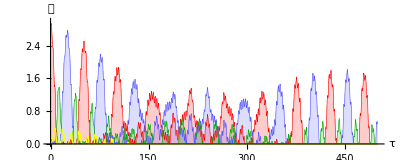

InterpolatingFunction::dmval: Input value {0.509836} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
(* Plot Formatting *)
Title="Non-Markovian System: {n=4, β=0.06, η=0.07, m=1, ω=1, Ω=1, γ=0.5}"; 
height=400;
width=1000;
PlotFormat={Joined->True, PlotRange->{0, 3}, ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width,  AxesLabel->{"τ", "𝒩"}, AxesStyle->Directive[Black,23], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 25], PlotLabel->None, PlotStyle->{Thickness[0.0010]}};
(* Plot LN Data of the System *)
LNPlot=ListPlot[{LNDataeta007[[1]], LNDataeta007[[2]], LNDataeta007[[3]], LNDataeta007[[6]]}, Evaluate[PlotFormat], (* PlotLegends->{"LN12", "LN13 = LN24", "LN14 = LN23", "LN34"},*) Filling->Bottom];

(* Data order should be LN34 (Red), LN12 (Blue), LN14=LN23 (Green), LN13=LN24 (Yellow) *)
LNPlot2=ListLinePlot[{LNDataeta007[[6]], LNDataeta007[[1]], LNDataeta007[[3]], LNDataeta007[[2]]}, PlotStyle->{Directive[Red, Thickness[0.0010]], Directive[Lighter[Blue], Thickness[0.0010]], Directive[Darker[Green], Thickness[0.0010]], Directive[Yellow, Thickness[0.0020]]}, Evaluate[PlotFormat], (* PlotLegends->{"LN12", "LN13 = LN24", "LN14 = LN23", "LN34"},*) Filling->Bottom]

(* Data order should be LN34 (Red), LN12 (Blue), LN14=LN23 (Green), LN13=LN24 (Yellow) *)

LNPLotwithEnvelopFunc=Rasterize[Show[LNPlot2, Plot[EnvelopFunc[x], {x, 0.5, 482}, PlotStyle->Directive[Dashed, Gray], PlotRange->All]]]
```

```mathematica
Export["Non-Markovian System Eta 0.07.png", LNPLotwithEnvelopFunc]
```

Non-Markovian System Eta 0.07.png